### a×bc=de

```mathematica
unique[L_]:=Select[L,Count[L[[All,1]],#[[1]]]==1&]
```

```mathematica
all=Flatten[Table[{a,b,c}~Join~IntegerDigits[a (10b+ c)],{a,0,9},{b,1,9},{c,0,9}],2];
```

```mathematica
all5=Select[all,Length[#]==5&];
```

```mathematica
sol=Select[unique[Sort[Map[{#[[1]]-#[[2]],#}&,Select[Tuples[all5,2],Max[Abs[#[[1]]-#[[2]]]]==1&]]]],#[[1,1]]<1&]
```

{{{-1,1,-1,-1,-1},{{2,3,8,7,6},{3,2,9,8,7}}},{{-1,1,-1,0,-1},{{2,2,8,5,6},{3,1,9,5,7}}},{{-1,1,-1,0,0},{{2,2,7,5,4},{3,1,8,5,4}}},{{-1,1,-1,0,1},{{2,2,6,5,2},{3,1,7,5,1}}},{{-1,1,-1,1,-1},{{3,2,7,8,1},{4,1,8,7,2}}},{{-1,1,-1,1,0},{{3,2,6,7,8},{4,1,7,6,8}}},{{-1,1,-1,1,1},{{3,2,5,7,5},{4,1,6,6,4}}},{{-1,1,0,0,1},{{2,2,9,5,8},{3,1,9,5,7}}},{{-1,1,0,1,1},{{3,2,9,8,7},{4,1,9,7,6}}},{{-1,1,1,1,-1},{{2,2,4,4,8},{3,1,3,3,9}}},{{-1,1,1,1,0},{{2,2,3,4,6},{3,1,2,3,6}}}}

```mathematica
ind={1,3,4,6,7};
```

```mathematica
pic[L_,q_]:=Graphics[{Table[Line[{{0,i},{q,i}}],{i,0,3}],Table[Line[{{i,j},{i,j+1}}],{i,0,q},{j,0,2,2}],Table[Text["×",{ii-.5,jj+.5}],{ii,Most[Complement[Range[q],ind]]},{jj,0,2,2}],Text["=",{Last[Complement[Range[q],ind]]-.5,.5}],Text["=",{Last[Complement[Range[q],ind]]-.5,2.5}],MapIndexed[Which[#1==-1,Text["⋀",{ind[[#2[[1]]]]-.5,1.6}],#1==1,Text["⋁",{ind[[#2[[1]]]]-.5,1.6}],True,Text["‖",{ind[[#2[[1]]]]-.5,1.6}]]&,L[[1]]]},ImageSize->15q]
```

```mathematica
picc[L_,q_]:=Graphics[{Table[Line[{{0,i},{q,i}}],{i,0,3}],Table[Line[{{i,j},{i,j+1}}],{i,0,q},{j,0,2,2}],Table[Text["×",{ii-.5,jj+.5}],{ii,Most[Complement[Range[q],ind]]},{jj,0,2,2}],Text["=",{Last[Complement[Range[q],ind]]-.5,.5}],Text["=",{Last[Complement[Range[q],ind]]-.5,2.5}],MapIndexed[Which[#1==-1,Text["⋀",{ind[[#2[[1]]]]-.5,1.6}],#1==1,Text["⋁",{ind[[#2[[1]]]]-.5,1.6}],True,Text["‖",{ind[[#2[[1]]]]-.5,1.6}]]&,L[[1]]],MapIndexed[Text[#1,{ind[[#2[[2]]]]-1/2,9/2-2#2[[1]]}]&,L[[2]],{2}]},ImageSize->15q]
```

```mathematica
Map[{pic[#,7],picc[#,7]}&,sol]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### a×b×c=def

```mathematica
all=Flatten[Table[{a,b,c}~Join~IntegerDigits[a b c],{a,0,9},{b,0,9},{c,0,9}],2];
```

```mathematica
all6=Select[all,Length[#]==6&];
```

```mathematica
sol=Select[unique[Sort[Map[{#[[1]]-#[[2]],#}&,Select[Tuples[all6,2],Max[Abs[#[[1]]-#[[2]]]]==1&]]]],#[[1,1]]<1&]
```

{{{-1,-1,-1,-1,1,-1},{{5,5,5,1,2,5},{6,6,6,2,1,6}}},{{-1,-1,1,0,-1,-1},{{7,7,5,2,4,5},{8,8,4,2,5,6}}},{{-1,1,-1,0,-1,-1},{{7,5,7,2,4,5},{8,4,8,2,5,6}}},{{-1,1,1,0,1,1},{{4,8,8,2,5,6},{5,7,7,2,4,5}}}}

```mathematica
ind={1,3,5,7,8,9};
```

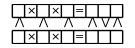
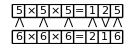
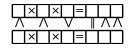
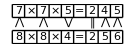
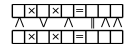
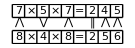
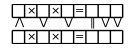
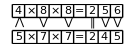

```mathematica
Map[{pic[#,9],picc[#,9]}&,sol]
```

### a×b×c×d=efg and a×b×c×d=efgh

```mathematica
all=Flatten[Table[{a,b,c,d}~Join~IntegerDigits[a b c d],{a,0,9},{b,0,9},{c,0,9},{d,0,9}],3];
```

```mathematica
all7=Select[all,Length[#]==7&];
all8=Select[all,Length[#]==8&];
```

```mathematica
Select[sol=unique[Sort[Map[{#[[1]]-#[[2]],#}&,Select[Tuples[all7,2],Max[Abs[#[[1]]-#[[2]]]]==1&]]]],#[[1,1]]<1&];
```

```mathematica
ind={1,3,5,7,9,10,11};
```

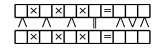
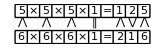
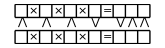
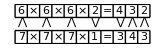
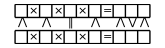
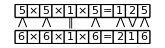
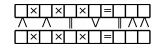
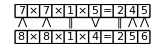

```mathematica
Map[{pic[#,11],picc[#,11]}&,sol]
```

```mathematica
sol=Select[unique[Sort[Map[{#[[1]]-#[[2]],#}&,Select[Tuples[all8,2],Max[Abs[#[[1]]-#[[2]]]]==1&]]]],#[[1,1]]<1&];
```

```mathematica
ind={1,3,5,7,9,10,11,12};
```

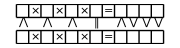
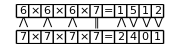
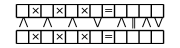
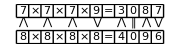
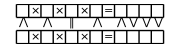
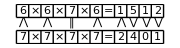
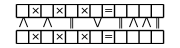
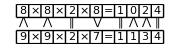
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Map[{pic[#,12],picc[#,12]}&,sol]
```

### a×b×cd=ef and a×b×cd=efg and a×b×cd=efgh

```mathematica
all=Flatten[Table[{a,b,c,d}~Join~IntegerDigits[a b (10c +d)],{a,0,9},{b,0,9},{c,1,9},{d,0,9}],3];
```

```mathematica
all6=Select[all,Length[#]==6&];
all7=Select[all,Length[#]==7&];
all8=Select[all,Length[#]==8&];
```

```mathematica
sol=Select[unique[Sort[Map[{#[[1]]-#[[2]],#}&,Select[Tuples[all6,2],Max[Abs[#[[1]]-#[[2]]]]==1&]]]],#[[1,1]]<1&];
```

```mathematica
ind={1,3,5,6,8,9};
```

```mathematica
Map[{pic[#,9],picc[#,9]}&,sol]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
sol=Select[unique[Sort[Map[{#[[1]]-#[[2]],#}&,Select[Tuples[all7,2],Max[Abs[#[[1]]-#[[2]]]]==1&]]]],#[[1,1]]<1&];
```

```mathematica
ind={1,3,5,6,8,9,10};
```

```mathematica
Map[{pic[#,10],picc[#,10]}&,sol]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
sol=Select[unique[Sort[Map[{#[[1]]-#[[2]],#}&,Select[Tuples[all8,2],Max[Abs[#[[1]]-#[[2]]]]==1&]]]],#[[1,1]]<1&];
```

```mathematica
ind={1,3,5,6,8,9,10,11};
```

```mathematica
Map[{pic[#,11],picc[#,11]}&,sol]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}